```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["results/"<>temp<>".dat",res];];

import[res_]:=res=Import["results/"<>ToString[res]<>".dat"];
```

## Charmonium s-wave

### Import Data

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Do[ccdata[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[ccdatau[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[ccdatal[n]=Import["cc/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscancorig]];
Quiet[fit[ccdatal,ccmodell,Tscancorig]];
Quiet[fit[ccdatau,ccmodelu,Tscancorig]];
```

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];
If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];
If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitcc];
import[wrfitccl];
import[wrfitccu];
import[gfitcc];
import[gfitccl];
import[gfitccu];
import[cfitcc];
import[cfitccl];
import[cfitccu];
import[dfitcc];
import[dfitccl];
import[dfitccu];
import[sfitcc];
import[sfitccl];
import[sfitccu];
import[s2fitcc];
import[s2fitccl];
import[s2fitccu];
import[areafitcc];
import[areafitccl];
import[areafitccu];
```

```mathematica
cc1Tcut=1;
Do[If[Length[wrfitcc[[-i]]]<2,cc1Tcut=Length[wrfitcc]-i];,{i,Length[wrfitcc]}];
cc1uTcut=1;
Do[If[Length[wrfitccu[[-i]]]<2,cc1uTcut=Length[wrfitccu]-i];,{i,Length[wrfitccl]}];
cc1lTcut=1;Do[If[Length[wrfitccl[[-i]]]<2,cc1lTcut=Length[wrfitccl]-i];,{i,Length[wrfitccu]}];
```

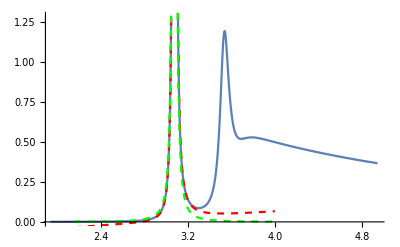

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

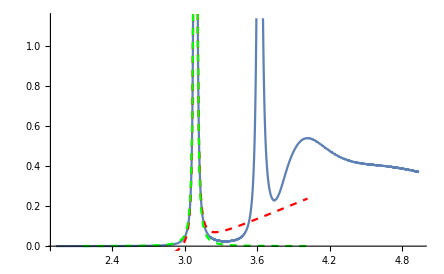

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

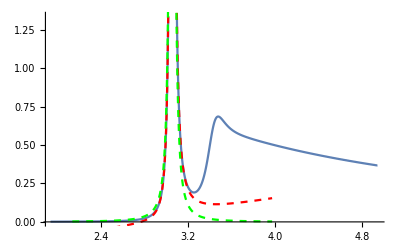

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
cccont={3.5997520612412757,3.5793607467267003,3.560301558921498,3.5424236239883413,3.5255990093879177,3.5097184240792423,3.4946878665615357,3.4804259850015464,3.4668619695502088,3.453933854385287,3.441587146150098,3.418450833828849,3.3870648251104365,3.3589397640966334,3.333461845319096,3.3101688347391254,3.288705052974616,3.2687916938092028,3.2502066638496983,3.232770531355081,3.2163365119506206,3.200783186465342,3.1860091122188536,3.171928771838143,3.158469484027324,3.1458184742331334,3.134060322128044,3.122685386837357,3.1116630509021292,3.1009661138249194,3.090570312280476,3.0804539213291253,3.070597419465198,3.0609832063360436,3.051595363642566,3.042419451430226,3.033442335516478,3.024652037212438,3.0160376007774596,3.007588988677513,2.999296978294029,2.99115307862333,2.983149459600338,2.9752788806165733,2.967534639380122,2.9599105171523417,2.952400734651447,2.9449999143839545,2.937703040709472,2.930505433584058,2.9234027146777617,2.9163907866775034,2.909465806756744,2.902624168316153,2.895862481204349,2.8891775561701127,2.8825663863863156,2.876026139351732};
cccontl={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7331563354692356,3.712514410706986,3.6748691903270925,3.625793822843574,3.5835878590815318,3.5466662939243827,3.513913516857778,3.4845186616210144,3.457876395570456,3.433524495719609,3.411103115430383,3.3903273707138517,3.3709683877773813,3.3528398922862284,3.335788522820287,3.319686705655616,3.3047727566323406,3.291140659350383,3.2780711605994313,3.2655141508656347,3.2534256749292476,3.241766987875234,3.230503783620591,3.2196055579371228,3.2090450798878205,3.198797950577609,3.1888422324213757,3.1791581383637855,3.169727765460862,3.160534863846772,3.15156465220645,3.1428036428072406,3.1342394994001648,3.125860916999752,3.1176575047964237,3.109619699565007,3.101738677131591,3.0940062803985513,3.086414957900857,3.0789577010216904,3.0716280007825425,3.064419795679852,3.0573274380484783,3.0503456535090536,3.043469512139379,3.036694398230153,3.0300159862040177,3.0234302130492474,3.0169332650276273};
cccontu={3.398436526578907,3.38409432231057,3.370481061901545,3.3575281861265385,3.345175914463943,3.333371844963344,3.3220698199520213,3.311229000986615,3.300813103243876,3.290789757718314,3.2811299822659414,3.2627995655639532,3.237456925795425,3.214284138245178,3.1929173953434944,3.173073968377218,3.1545302747434136,3.137106800095161,3.120657476716233,3.1050620382669747,3.09022041307245,3.076048540863171,3.06247520479034,3.0494395992420498,3.036889439342897,3.024984636692081,3.013800803069826,3.0029225154332306,2.992326954999799,2.981993704279212,2.97190442763462,2.962042603287172,2.9523932960015906,2.942942963825915,2.9336792930344657,2.9245910563699895,2.9156679922633,2.906900698646717,2.898280538332317,2.889799564858944,2.8814504474821403,2.873226411011175,2.8651211846773528,2.8571289492264538,2.849244299826176,2.841462205231684,2.833777975088651,2.826187231968362,2.818685881140122,2.811270091134757,2.803936267822333,2.7966810389495573,2.789501233758976,2.78239386912829,2.775356134349964,2.7683853791962925,2.7614790995770355,2.7546349313709397};
```

```mathematica
Export["plots/cc_Econt.dat",Transpose[{Tscancorig,cccont,cccontl,cccontu}]]
```

plots/cc_Econt.dat

```mathematica
ccbind=cccont-wrfitcc;
ccbindu=cccontu-wrfitccu;
ccbindl=cccontl-wrfitccl;
```

```mathematica
Do[If[(ccbind-gfitcc)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitcc)[[i,2]]>0,cc2Tmelt=i,cc2Tmelt=1],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccl)[[i,2]]>0,cc2lTmelt=i,cc2lTmelt=1],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

```mathematica
N[{Tscancorig[[cc1lTmelt]],Tscancorig[[cc1Tmelt]],Tscancorig[[cc1uTmelt]]}/0.155]
```

{1.93548,1.72258,1.49032}

```mathematica
N[{Tscancorig[[cc1lTmelt]],Tscancorig[[cc1Tmelt]],Tscancorig[[cc1uTmelt]]}/0.155]
```

{1.66452,1.39355,1.21935}

```mathematica
N[{Tscancorig[[cc2lTmelt]],Tscancorig[[cc2Tmelt]],Tscancorig[[cc2uTmelt]]}/0.155]
```

{0.967742,0.967742,0.967742}

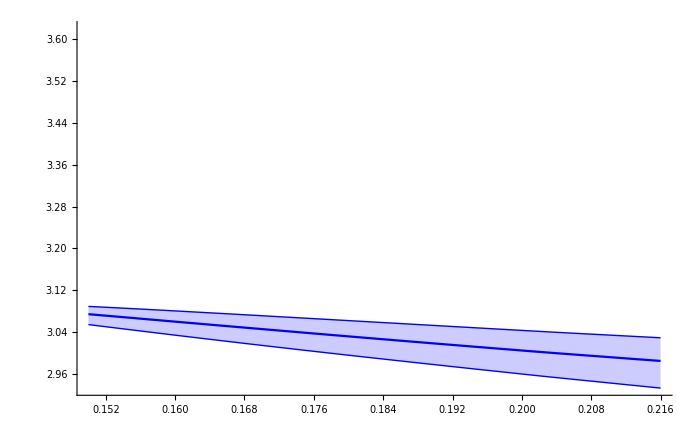

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],wrfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],wrfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

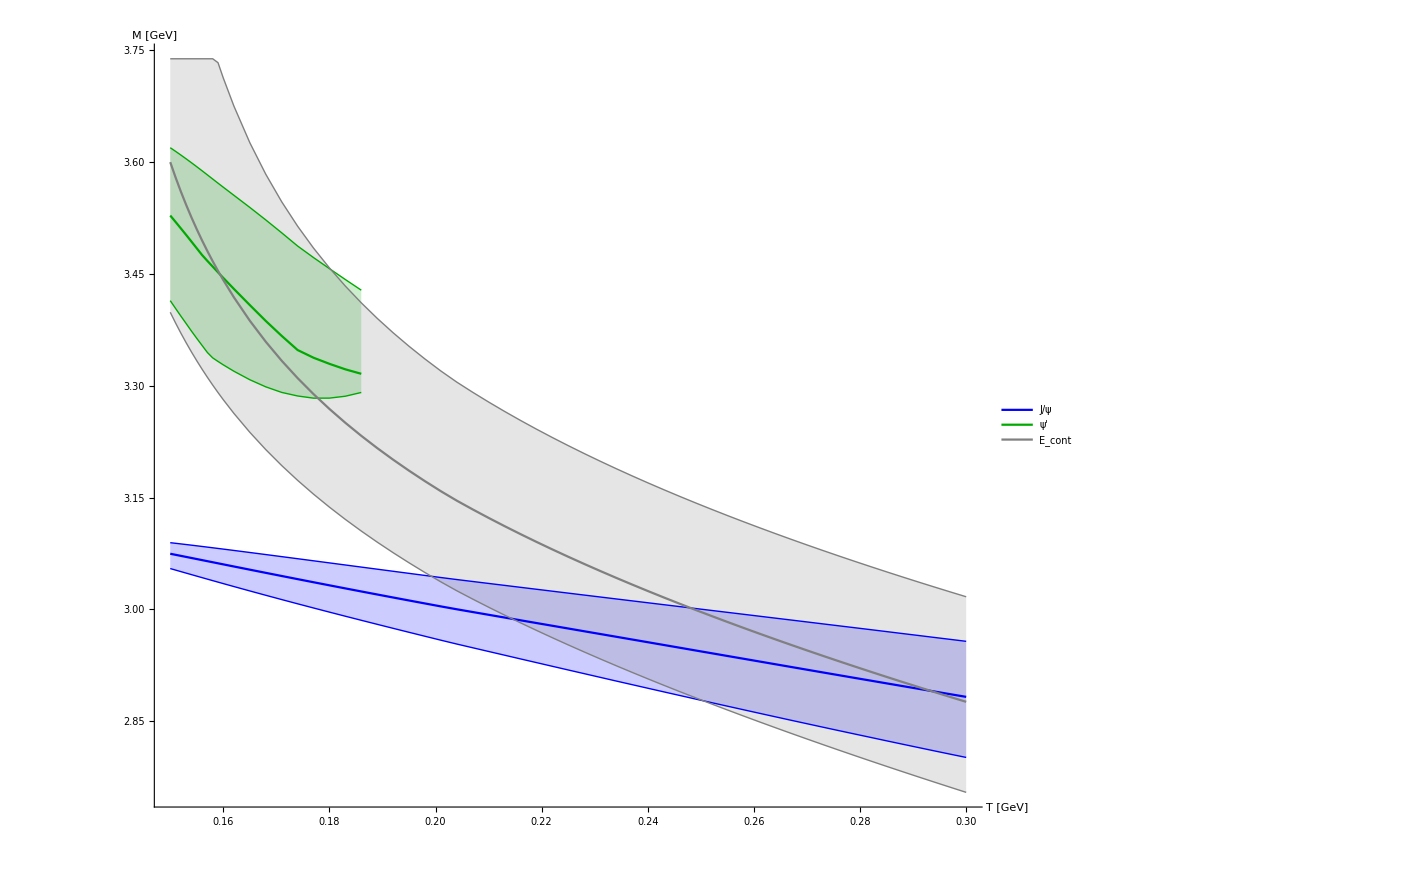

```mathematica
ListPlot[{Transpose[{Tscancorig,wrfitcc[[All,1]]}],Transpose[{Tscancorig,wrfitccl[[All,1]]}],Transpose[{Tscancorig,wrfitccu[[All,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitcc[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccl[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitccu[[;;cc1uTcut-1,2]]}],Transpose[{Tscancorig,cccont}],Transpose[{Tscancorig,cccontu}],Transpose[{Tscancorig,cccontl}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"],None,None,Style["E_cont",25,"Helvetica"]}],{0.8,0.8}]]
```

```mathematica
Export["plots/Jpsi_mass.dat",Transpose[{Tscancorig,wrfitcc[[All,1]],wrfitccl[[All,1]],wrfitccu[[All,1]]}]]
```

plots/Jpsi_mass.dat

```mathematica
Export["plots/psip_mass.dat",Transpose[{Tscancorig[[;;cc1uTcut-1]],wrfitcc[[;;cc1uTcut-1,2]],wrfitccl[[;;cc1uTcut-1,2]],wrfitccu[[;;cc1uTcut-1,2]]}]]
```

plots/psip_mass.dat

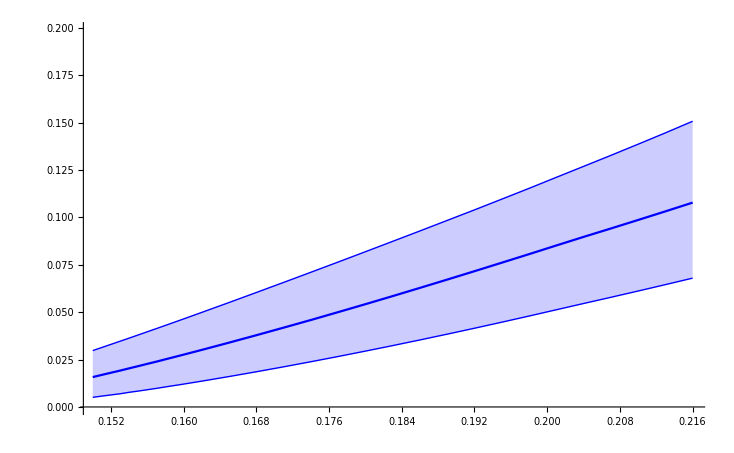

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],gfitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],gfitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],gfitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],gfitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

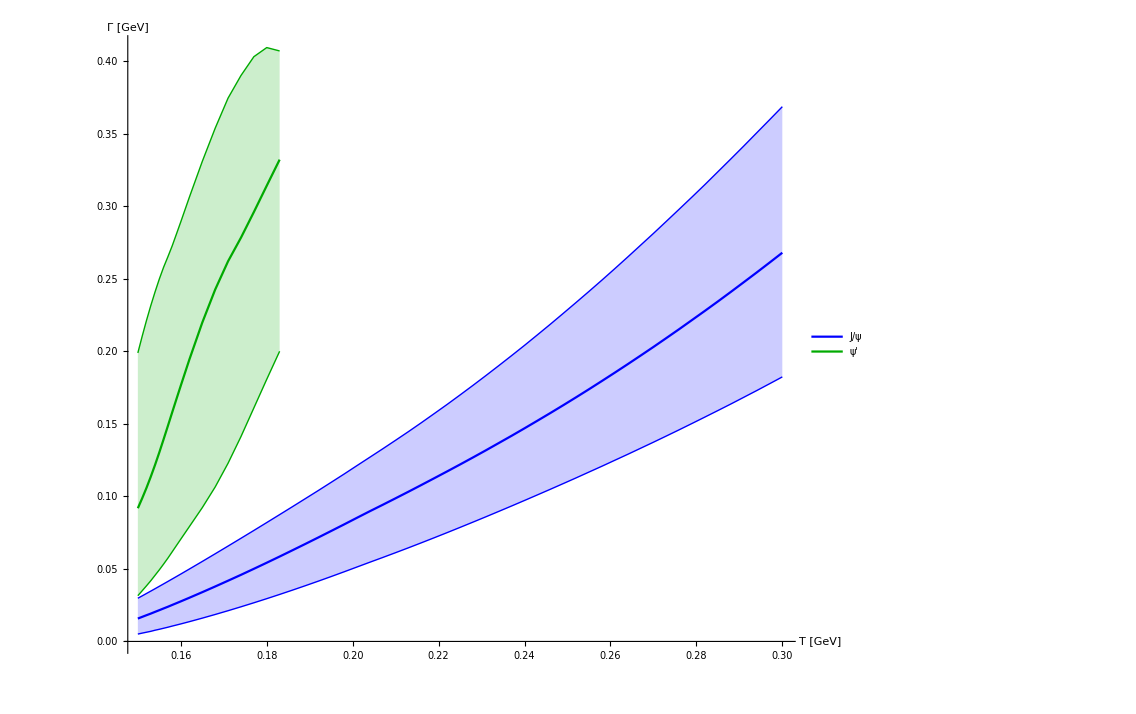

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;]],gfitcc[[;;,1]]}],Transpose[{Tscancorig[[;;]],gfitccl[[;;,1]]}],Transpose[{Tscancorig[[;;]],gfitccu[[;;,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitcc[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitccl[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitccu[[;;cc1uTcut-2,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

```mathematica
Export["plots/Jpsi_width.dat",Transpose[{Tscancorig,gfitcc[[All,1]],gfitccl[[All,1]],gfitccu[[All,1]]}]]
```

plots/Jpsi_width.dat

```mathematica
Export["plots/psip_width.dat",Transpose[{Tscancorig[[;;cc1uTcut-2]],gfitcc[[;;cc1uTcut-2,2]],gfitccl[[;;cc1uTcut-2,2]],gfitccu[[;;cc1uTcut-2,2]]}]]
```

plots/psip_width.dat

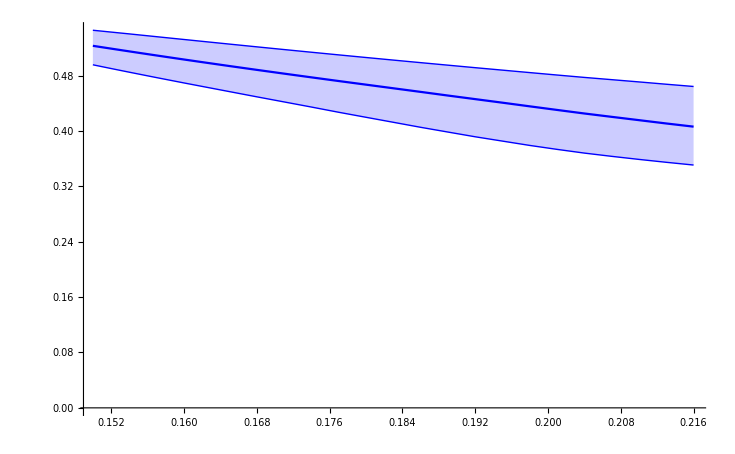

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;cc1Tmelt]],areafitcc[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],areafitccl[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc1Tmelt]],areafitccu[[;;cc1Tmelt,1]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitcc[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitccl[[;;cc2Tmelt,2]]}],Transpose[{Tscancorig[[;;cc2Tmelt]],areafitccu[[;;cc2Tmelt,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin}},Joined->True]
```

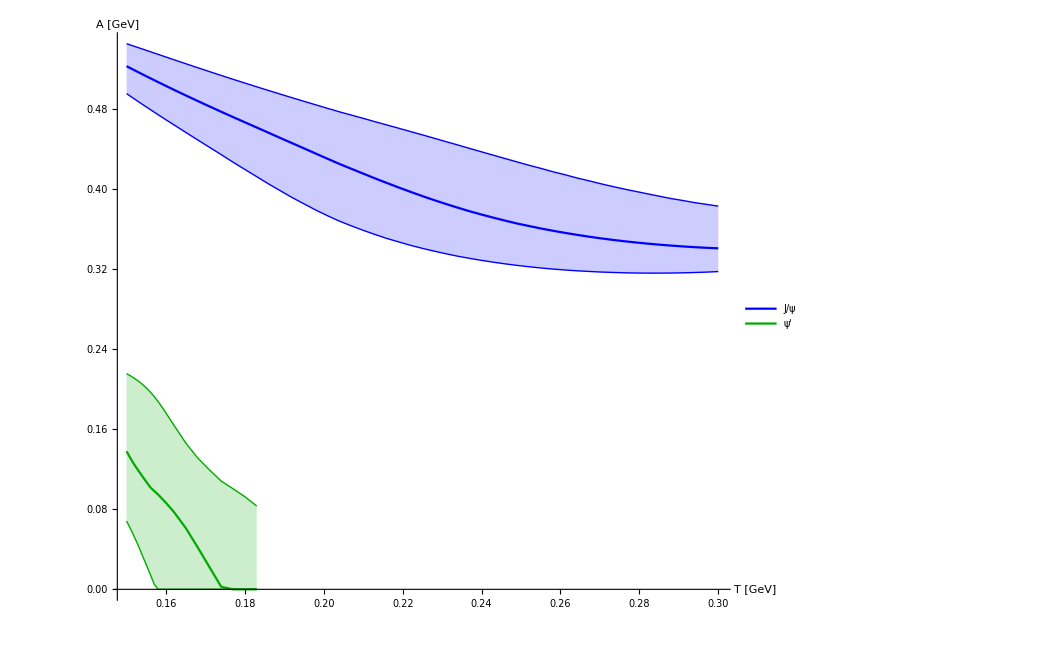

```mathematica
ListPlot[{Transpose[{Tscancorig[[;;]],areafitcc[[;;,1]]}],Transpose[{Tscancorig[[;;]],areafitccl[[;;,1]]}],Transpose[{Tscancorig[[;;]],areafitccu[[;;,1]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitcc[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitccl[[;;cc1uTcut-2,2]]}],Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitccu[[;;cc1uTcut-2,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["A [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

```mathematica
Export["plots/Jpsi_area.dat",Transpose[{Tscancorig,areafitcc[[All,1]],areafitccl[[All,1]],areafitccu[[All,1]]}]]
```

plots/Jpsi_area.dat

```mathematica
Export["plots/psip_area.dat",Transpose[{Tscancorig[[;;cc1uTcut-2]],areafitcc[[;;cc1uTcut-2,2]],areafitccl[[;;cc1uTcut-2,2]],areafitccu[[;;cc1uTcut-2,2]]}]]
```

plots/psip_area.dat

## Charmonium p-wave

### Import Data

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Tscanpwave=Table[x,{x,0.15,0.19,0.001}]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19}

```mathematica
Do[ccdata[n]=Import["cc/pwccT"<>ToString[Round[1000Tscanpwave[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanpwave]}];
```

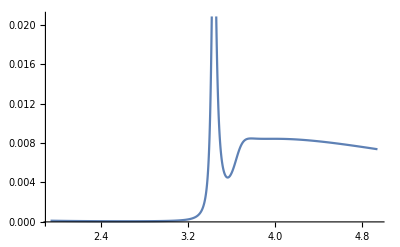

```mathematica
Block[{n=1},ListPlot[ccdata[n],Joined->True]]
```

```mathematica
Do[ccdatau[n]=Import["cc/pwccT"<>ToString[Round[1000Tscanpwave[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanpwave]}];
```

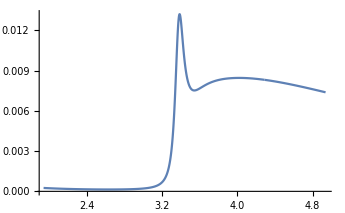

```mathematica
Block[{n=2},ListPlot[ccdatau[n],Joined->True]]
```

```mathematica
Do[ccdatal[n]=Import["cc/pwccT"<>ToString[Round[1000Tscanpwave[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanpwave]}];
```

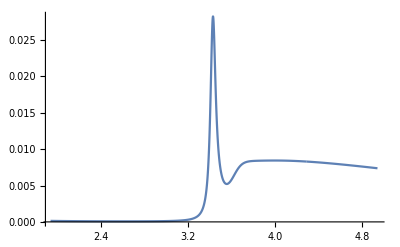

```mathematica
Block[{n=3},ListPlot[ccdata[n],Joined->True]]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscanpwave]];
Quiet[fit[ccdatal,ccmodell,Tscanpwave]];
Quiet[fit[ccdatau,ccmodelu,Tscanpwave]];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

### Store Results

```mathematica
Do[If[Length[ccmodel[[i]]]>2,ccmodel[[i]]=ccmodel[[i,;;2]]];
If[Length[ccmodelu[[i]]]>2,ccmodelu[[i]]=ccmodelu[[i,;;2]]];
If[Length[ccmodell[[i]]]>2,ccmodell[[i]]=ccmodell[[i,;;2]]];,{i,Length[ccmodel]}];
```

```mathematica
Clear[wrfitccp,wrfitccpl,wrfitccpu,gfitccp,gfitccpl,gfitccpu,areafitccp,areafitccpu,areafitccpl,cfitccp,cfitccpl,cfitccpu,dfitccp,dfitccpl,dfitccpu,sfitccp,sfitccpl,sfitccpu,s2fitccp,s2fitccpl,s2fitccpu];
```

```mathematica
store[wr,wrfitccp,ccmodel];
store[wr,wrfitccpl,ccmodell];
store[wr,wrfitccpu,ccmodelu];
store[Γ,gfitccp,ccmodel];
store[Γ,gfitccpl,ccmodell];
store[Γ,gfitccpu,ccmodelu];
store[const,cfitccp,ccmodel];
store[const,cfitccpl,ccmodell];
store[const,cfitccpu,ccmodelu];
store[δbg,dfitccp,ccmodel];
store[δbg,dfitccpl,ccmodell];
store[δbg,dfitccpu,ccmodelu];
store[shift,sfitccp,ccmodel];
store[shift,sfitccpl,ccmodell];
store[shift,sfitccpu,ccmodelu];
store[shift2,s2fitccp,ccmodel];
store[shift2,s2fitccpl,ccmodell];
store[shift2,s2fitccpu,ccmodelu];
storearea[areafitccp,ccmodel];
storearea[areafitccpl,ccmodell];
storearea[areafitccpu,ccmodelu];
```

### Display Results

```mathematica
import[wrfitccp];
import[wrfitccpl];
import[wrfitccpu];
import[gfitccp];
import[gfitccpl];
import[gfitccpu];
import[cfitccp];
import[cfitccpl];
import[cfitccpu];
import[dfitccp];
import[dfitccpl];
import[dfitccpu];
import[sfitccp];
import[sfitccpl];
import[sfitccpu];
import[s2fitccp];
import[s2fitccpl];
import[s2fitccpu];
import[areafitccp];
import[areafitccpl];
import[areafitccpu];
```

```mathematica
cc1Tcut=1;
Do[If[Length[wrfitccp[[-i]]]<2,cc1Tcut=Length[wrfitccp]-i];,{i,Length[wrfitccp]}];
cc1uTcut=1;
Do[If[Length[wrfitccpu[[-i]]]<2,cc1uTcut=Length[wrfitccpu]-i];,{i,Length[wrfitccpl]}];
cc1lTcut=1;Do[If[Length[wrfitccpl[[-i]]]<2,cc1lTcut=Length[wrfitccpl]-i];,{i,Length[wrfitccpu]}];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/100}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

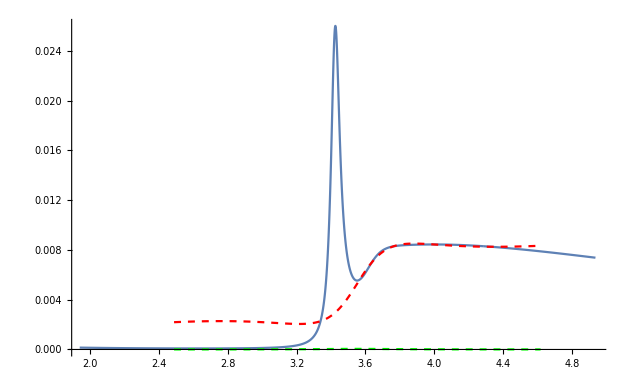

```mathematica
Block[{i=4,ii=2},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],dfitccp[[i,ii]],cfitccp[[i,ii]],sfitccp[[i,ii]],s2fitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],cfitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

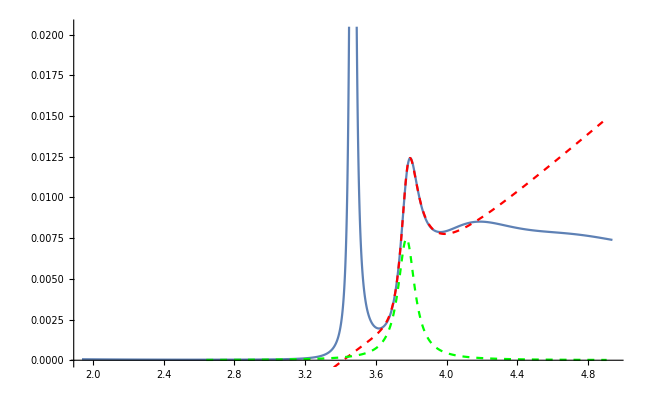

```mathematica
Block[{i=6,ii=2},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],dfitccpl[[i,ii]],cfitccpl[[i,ii]],sfitccpl[[i,ii]],s2fitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],cfitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

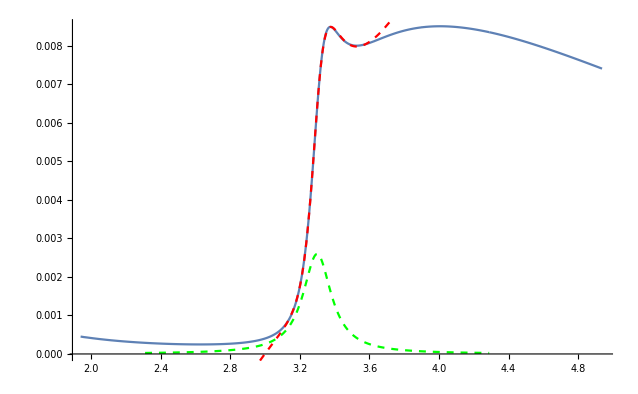

```mathematica
Block[{i=15,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],dfitccpu[[i,ii]],cfitccpu[[i,ii]],sfitccpu[[i,ii]],s2fitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],cfitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
cccont={3.5997520612412757,3.5793607467267003,3.560301558921498,3.5424236239883413,3.5255990093879177,3.5097184240792423,3.4946878665615357,3.4804259850015464,3.4668619695502088,3.453933854385287,3.441587146150098,3.42977370754927,3.418450833828849,3.407580485272377,3.3971286520766286,3.3870648251104365,3.3773615424086576,3.3679940066685576,3.3589397640966343,3.3501784277157043,3.3416914352969487,3.333461845319096,3.3254741620390114,3.3177141770834644,3.310168834739126,3.3028261173445284,3.295674938846256,3.288705052974616,3.281906975967159,3.2752719129315073,3.2687916938092028,3.26245872012757,3.2562659119676933,3.2502066638496983,3.244274805077199,3.23846456331404,3.232770531355081,3.2271876382940294,3.221711123560593,3.2163365119506206,3.2110595919911713};
cccontl={3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.738379532206608,3.7331563354692356,3.712514410706986,3.6931289067792497,3.6748691903270925,3.657622868203566,3.641292645011792,3.6257938228435744,3.6110522772319458,3.597002818378722,3.583587859081532,3.5707563147360624,3.5584626846858187,3.5466662939243827,3.5353306598323986,3.5244229480657028,3.5139135168577784,3.5037755339721213,3.493984639929561,3.4845186616210144,3.4753573710340717,3.4664822683663266,3.457876395570456,3.4495241793363602,3.441411285421246,3.433524495719609,3.4258515998393726,3.418381298173664,3.411103115430383,3.4040073255274725,3.397084884872211,3.3903273707138517,3.3837269274809714};
cccontu={3.398436526578907,3.38409432231057,3.370481061901545,3.3575281861265385,3.345175914463943,3.333371844963344,3.3220698199520213,3.311229000986615,3.300813103243876,3.290789757718314,3.2811299822659414,3.271807740457743,3.2627995655639532,3.254084239592208,3.24564252302531,3.237456925795426,3.2295115047598553,3.2217916900976764,3.214284138245179,3.2069766024267214,3.1998578162436493,3.1929173953434944,3.186145752377599,3.179534017095313,3.173073968377218,3.166757976554575,3.160578947576004,3.1545302747434136,3.1486057986151668,3.1427997669958803,3.137106800095161,3.1315218621863337,3.1260402316743248,3.120657476716233,3.115369433082437,3.1101721834531566,3.1050620382669747,3.1000355192225117,3.0950893443270133,3.09022041307245,3.085425793709046};
```

```mathematica
Export["plots/chic_Econt.dat",Transpose[{Tscanpwave,cccont,cccontl,cccontu}]]
```

plots/chic_Econt.dat

```mathematica
ccbind=cccont-wrfitccp;
ccbindu=cccontu-wrfitccpu;
ccbindl=cccontl-wrfitccpl;
```

```mathematica
Do[If[(ccbind-gfitccp)[[i,1]]>0,cc1Tmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbind-gfitccp)[[i,2]]>0,cc2Tmelt=i,cc2Tmelt=1],{i,1,cc1Tcut}];
Do[If[(ccbindl-gfitccpl)[[i,1]]>0,cc1lTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindl-gfitccpl)[[i,2]]>0,cc2lTmelt=i,cc2lTmelt=1],{i,1,cc1lTcut}];
Do[If[(ccbindu-gfitccpu)[[i,1]]>0,cc1uTmelt=i],{i,1,Length[ccbind]}];
Do[If[(ccbindu-gfitccpu)[[i,2]]>0,cc2uTmelt=i,cc2uTmelt=1],{i,1,cc1uTcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
N[{Tscancorig[[cc1lTmelt]],Tscancorig[[cc1Tmelt]],0}/0.155]
```

{1.33548,1.00645,0.}

```mathematica
N[{Tscancorig[[cc2lTmelt]],Tscancorig[[cc2Tmelt]],0}/0.155]
```

{0.967742,0.967742,0.}

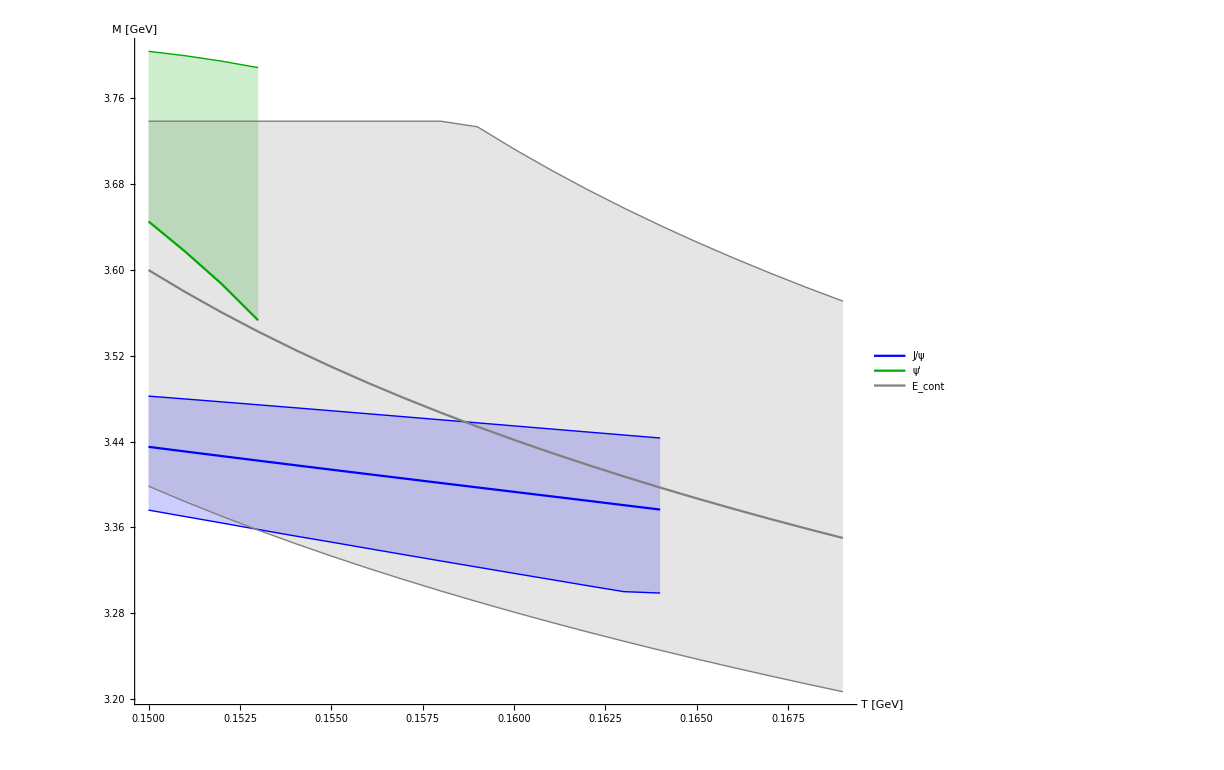

```mathematica
ListPlot[{Transpose[{Tscanpwave[[;;15]],wrfitccp[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],wrfitccpl[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],wrfitccpu[[;;15,1]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],wrfitccp[[;;cc1Tcut,2]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],wrfitccpl[[;;cc1Tcut,2]]}],Transpose[{Tscanpwave[[;;20]],cccont[[;;20]]}],Transpose[{Tscanpwave[[;;20]],cccontu[[;;20]]}],Transpose[{Tscanpwave[[;;20]],cccontl[[;;20]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},6->{7},6->{8}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"],None,None,Style["E_cont",25,"Helvetica"]},LegendLayout->"Row"],{0.5,0.9}]]
```

```mathematica
Export["plots/chic_mass.dat",Transpose[{Tscanpwave[[;;15]],wrfitccp[[;;15,1]],wrfitccpl[[;;15,1]],wrfitccpu[[;;15,1]]}]]
```

plots/chic_mass.dat

```mathematica
Export["plots/chic2_mass.dat",Transpose[{Tscanpwave[[;;4]],wrfitccp[[;;4,2]],wrfitccpl[[;;4,2]]}]]
```

plots/chic2_mass.dat

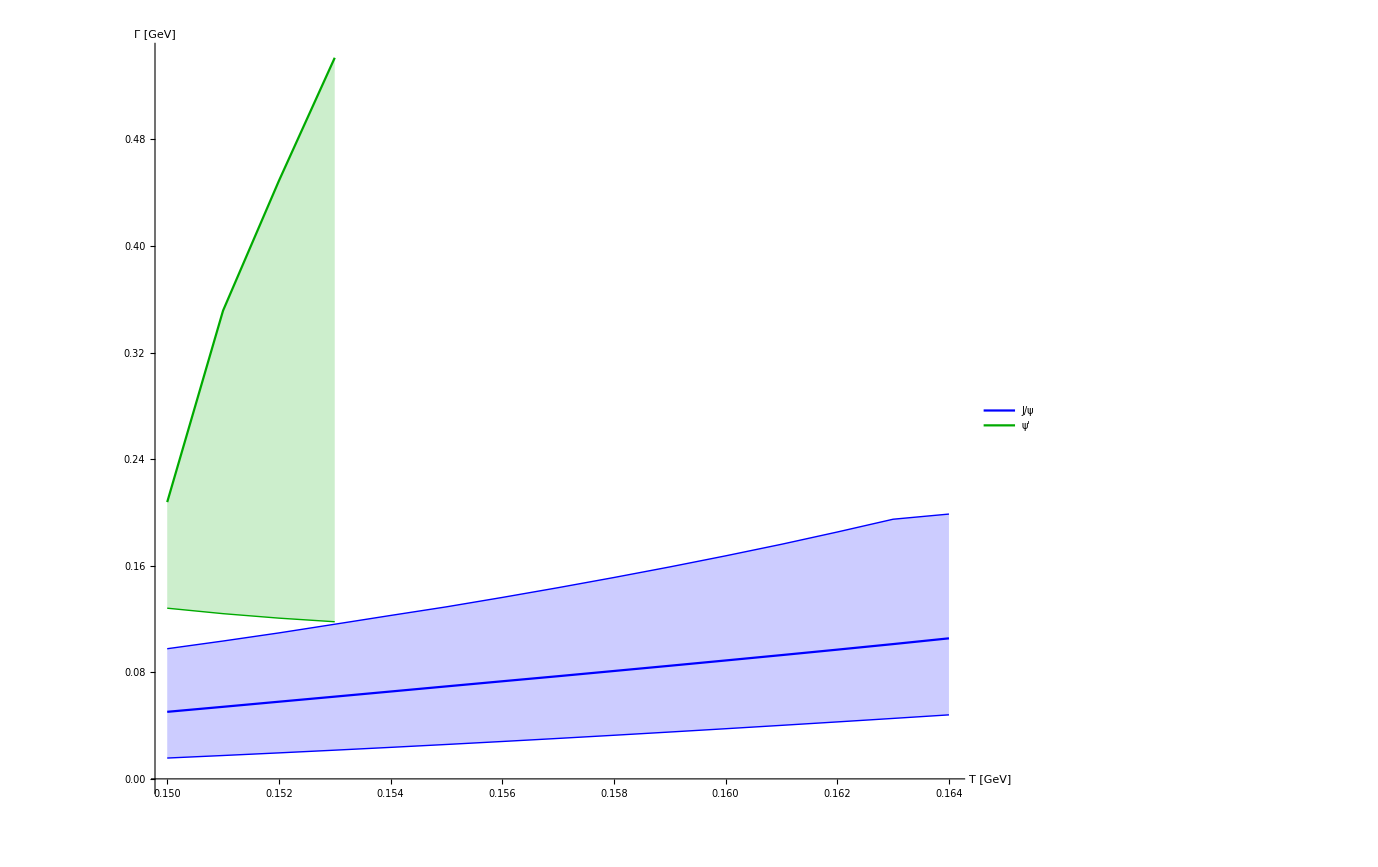

```mathematica
ListPlot[{Transpose[{Tscanpwave[[;;15]],gfitccp[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],gfitccpl[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],gfitccpu[[;;15,1]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],gfitccp[[;;cc1Tcut,2]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],gfitccpl[[;;cc1Tcut,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.6,0.75}]]
```

```mathematica
Export["plots/chic_width.dat",Transpose[{Tscanpwave[[;;15]],gfitccp[[;;15,1]],gfitccpl[[;;15,1]],gfitccpu[[;;15,1]]}]]
```

plots/chic_width.dat

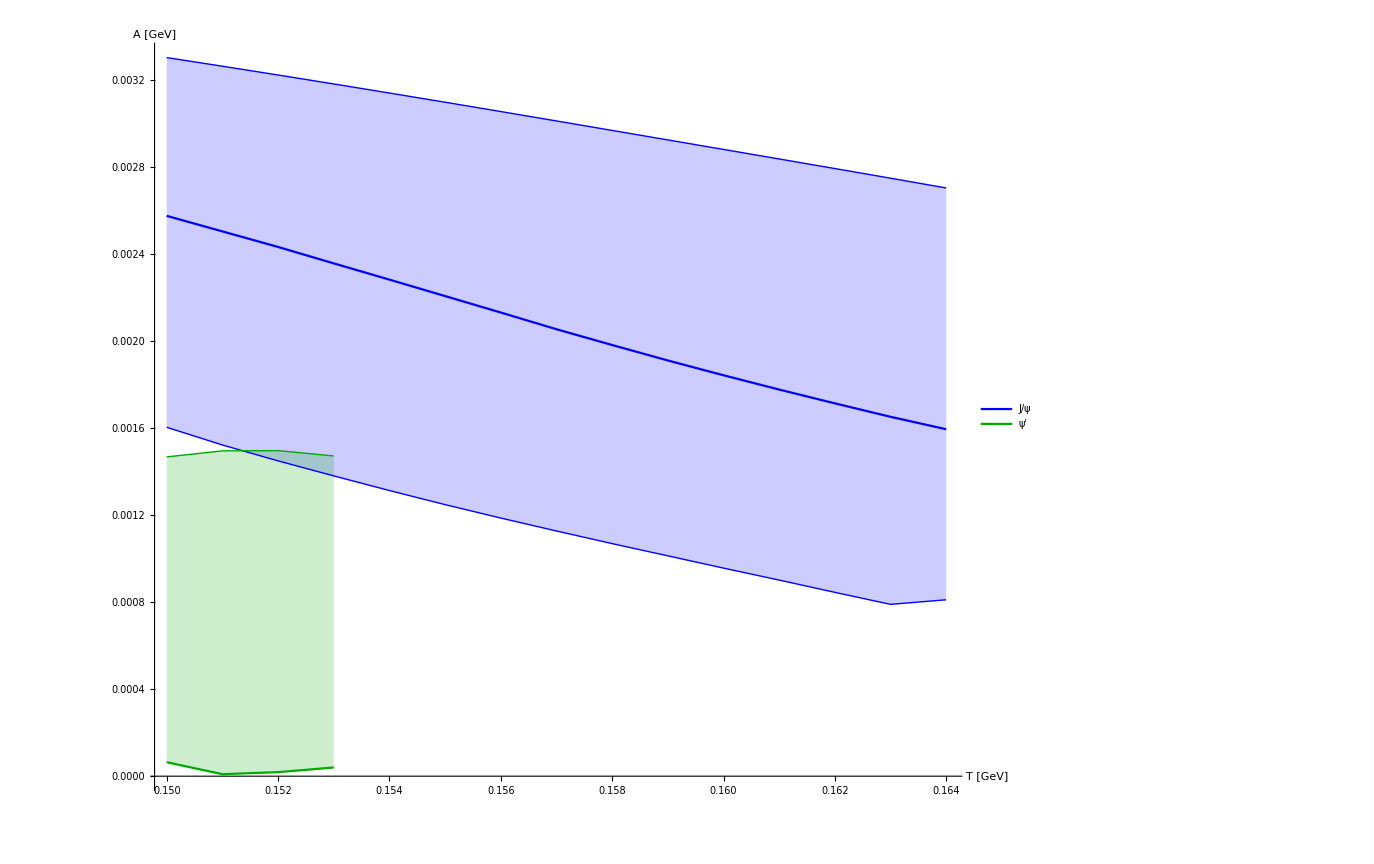

```mathematica
ListPlot[{Transpose[{Tscanpwave[[;;15]],areafitccp[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],areafitccpl[[;;15,1]]}],Transpose[{Tscanpwave[[;;15]],areafitccpu[[;;15,1]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],areafitccp[[;;cc1Tcut,2]]}],Transpose[{Tscanpwave[[;;cc1Tcut]],areafitccpl[[;;cc1Tcut,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin}},Joined->True,AxesLabel->{Style["T [GeV]",25,Black],Style["A [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

```mathematica
Export["plots/chic_area.dat",Transpose[{Tscanpwave[[;;15]],areafitccp[[;;15,1]],areafitccpl[[;;15,1]],areafitccpu[[;;15,1]]}]]
```

plots/chic_area.dat

## Bottomonium s-wave

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
Do[bbdata[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

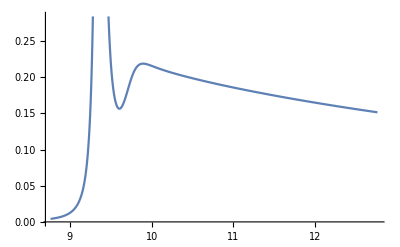

```mathematica
Block[{n=36},ListPlot[bbdata[n],Joined->True]]
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

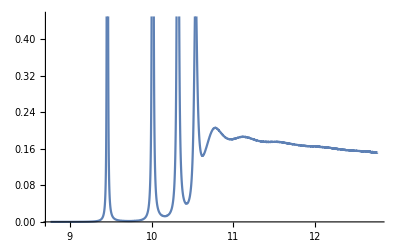

```mathematica
Block[{n=1},ListPlot[bbdatal[n],Joined->True]]
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscanborig]}];
```

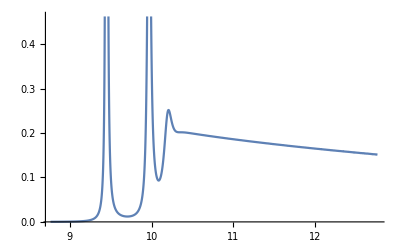

```mathematica
Block[{n=1},ListPlot[bbdatau[n],Joined->True]]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fit[bbdata,bbmodel,Tscanborig];
fit[bbdatau,bbmodelu,Tscanborig];
fit[bbdatal,bbmodell,Tscanborig];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
```

```mathematica
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbb];
import[wrfitbbl];
import[wrfitbbu];
import[gfitbb];
import[gfitbbl];
import[gfitbbu];
import[cfitbb];
import[cfitbbl];
import[cfitbbu];
import[dfitbb];
import[dfitbbl];
import[dfitbbu];
import[sfitbb];
import[sfitbbl];
import[sfitbbu];
import[s2fitbb];
import[s2fitbbl];
import[s2fitbbu];
import[areafitbb];
import[areafitbbl];
import[areafitbbu];
```

```mathematica
Do[If[Length[wrfitbb[[-i]]]<2,bb1Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<2,bb1uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<2,bb1lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<3,bb2Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];
Do[If[Length[wrfitbbu[[-i]]]<3,bb2uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];
Do[If[Length[wrfitbbl[[-i]]]<3,bb2lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
Do[If[Length[wrfitbb[[-i]]]<4,bb3Tcut=Length[wrfitbb]-i];,{i,Length[wrfitbb]}];Do[If[Length[wrfitbbu[[-i]]]<4,bb3uTcut=Length[wrfitbbu]-i];,{i,Length[wrfitbbu]}];Do[If[Length[wrfitbbl[[-i]]]<4,bb3lTcut=Length[wrfitbbl]-i];,{i,Length[wrfitbbl]}];
```

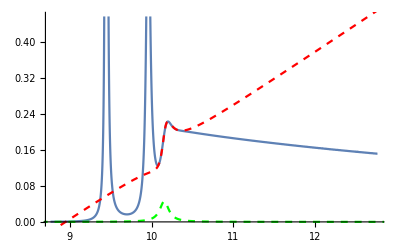

```mathematica
Block[{i=5,ii=3},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
fitONE[bbdata[5]]
```

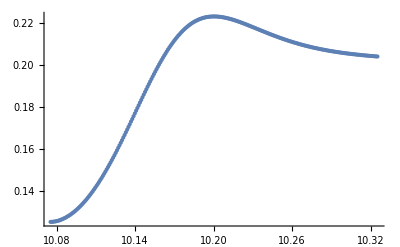

```mathematica
ListPlot[inputc[[2]]]
```

```mathematica
temp=NonlinearModelFit[inputc[[2]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[2]]},{Γ,gammas[[2]]},{const,maxys[[2]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000]
```

FittedModel[0.151031+0.000209435/(0.00459025+(-10.1549+w)^2)+0.121759 (-10.1549+w)+(0.00510649 (-10.1549+w))/(0.00459025+(-10.1549+w)^2)]

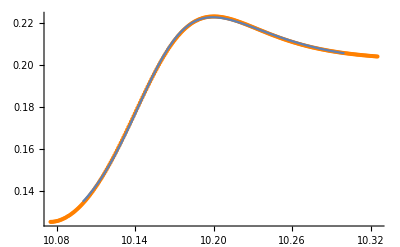

```mathematica
Show[ListPlot[inputc[[2]],PlotStyle->Orange],Plot[temp[x],{x,10.1,10.3}]]
```

```mathematica
bbmodel[[5]]=Append[bbmodel[[5]],temp]
```

{FittedModel[0.00278465+0.000326254/(0.0000215934+(-9.44607+w)^2)+0.00927724 (-9.44607+w)+(0.000872661 (-9.44607+w))/(0.0000215934+(-9.44607+w)^2)],FittedModel[0.0328142+0.000567841/(0.00074936+(-9.9565+w)^2)+0.183604 (-9.9565+w)+(0.00217863 (-9.9565+w))/(0.00074936+(-9.9565+w)^2)],FittedModel[0.151031+0.000209435/(0.00459025+(-10.1549+w)^2)+0.121759 (-10.1549+w)+(0.00510649 (-10.1549+w))/(0.00459025+(-10.1549+w)^2)]}

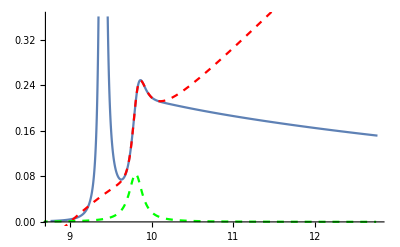

```mathematica
Block[{i=14,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

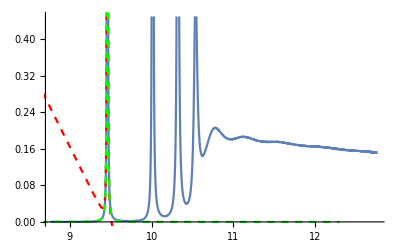

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
bbcont={10.425372529034668,10.335338891872635,10.26720761394349,10.212685292903828,10.16731190309034,10.12844658513792,10.094412161602595,10.064085031107432,10.036680059784564,10.011629580012245,9.988511409362781,9.96747493150493,9.94830585463075,9.930117625013263,9.912788610677097,9.89621788725859,9.88032087990969,9.865026073328908,9.85027250500583,9.836007821147573,9.82218675581476,9.80876992739373,9.795722877017155,9.783015293313008,9.770620382177347,9.758514350498022,9.74667598022245,9.735086274550136,9.723728161890362,9.712586248885195,9.701646607145124,9.690896596903944,9.680324715779712,9.669920465160457,9.659674238392858,9.649577225726656,9.639621326633844,9.629799077030688,9.62010358670188,9.610528479574953,9.601067846259276,9.59171619970901,9.582468434660354,9.573319795868064,9.564265844417333,9.555302432357605,9.546425677154614,9.537631939449463,9.528917804356869,9.520280061848183,9.511715692746593,9.50322185190471,9.494795857203327,9.486435175461619,9.478137413470805,9.469900306255262,9.461721709678878,9.453599590567686,9.445532020638552,9.43751716807023,9.429553292534763,9.421638737964178,9.413771928403195,9.40595136190288,9.39817560683909,9.390443296985117,9.382753127956226,9.375103853493824,9.367494281861074,9.359923273105196,9.352389735692185,9.344892624223434,9.337430936473433,9.330003711464334,9.322610026849764,9.315248997232757,9.307919771935948,9.300621533423119,9.293353495497186,9.286114901732196,9.278905024081087,9.27172316131876,9.264568637945787,9.25744080275282,9.250339027825161,9.243262707372196,9.23621125670242,9.229184111297064,9.222180725870718,9.21520057351252,9.2082431448733};
```

```mathematica
bbcontl={10.564,10.564,10.538134878500378,10.451414290636967,10.38408315247921,10.329396001765513,10.283496863363847,10.244001765967056,10.209347395274364,10.17846036007962,10.150575924029736,10.125783301889154,10.103691628392824,10.083026064660805,10.0635906909614,10.045226025730514,10.027800712906934,10.011205409690664,9.995348233254255,9.980151305382883,9.96554810063323,9.951481384793144,9.937901594485288,9.92476555037837,9.91203542569425,9.89967791218134,9.887663540362858,9.875966121302445,9.864562284557815,9.853431096172972,9.842553732821019,9.831913213856552,9.821494173620003,9.811282662459293,9.801265981005038,9.791432540150318,9.781771733326902,9.77227383082192,9.76292988945462,9.753731667153172,9.744671555225391,9.73574251556042,9.726938023444047,9.71825202304196,9.709678880314991,9.701213347852915,9.692850529503367,9.684585849718106,9.676415028020758,9.668334052019159,9.660339158621014,9.652426810913235,9.644593683661865,9.636836643977128,9.629152739675327,9.621539183195145,9.613993342149161,9.606512725790235,9.599094977403725,9.591737862727298,9.584439263880432,9.577197169385075,9.570009669215857,9.562874946371599,9.55579127247736,9.548757001076309,9.541770563201025,9.53483046254437,9.527935270673103,9.521083623751895,9.514274217935023,9.507505806735951,9.500777196923567,9.494087246399976,9.487434860527769,9.480818990316255,9.474238629310232,9.46769281180276,9.461180610441161,9.45470113425101,9.448253526999201,9.441836965013012,9.435450656099011,9.429093837437598,9.422765774585985,9.41646575988776,9.410193111182126,9.403947170733934,9.397727304013873,9.391532898635573,9.385363363348686};
```

```mathematica
bbcontu={10.2240569943723,10.158992312756736,10.106750450059334,10.063077393588818,10.02547828403704,9.992378444347967,9.962727267888553,9.93579265124655,9.911046261502438,9.88809567258373,9.866642279265756,9.846841692339327,9.828542983226622,9.811030614689248,9.794213116444213,9.778013763794982,9.762367624998802,9.747219298465957,9.732521166440108,9.718232023481189,9.704315991543202,9.690741652470745,9.677481348217105,9.664510611612391,9.651807699761754,9.639353208838784,9.627129753977336,9.615121701552368,9.603314943722339,9.591696709263008,9.580255399164331,9.56898045008858,9.557862216607003,9.546891866656232,9.536061293681653,9.525363041545416,9.51479023509536,9.504336522241534,9.493996023862598,9.483763286097428,9.473633242026082,9.463601175887447,9.453662690393244,9.44381368064604,9.434050307008865,9.424368974140133,9.41476631017905,9.405239148521106,9.39578451223081,9.38639959816022,9.377081764966086,9.367828519609809,9.35863750774142,9.349506502444981,9.340433396280435,9.331416191937214,9.322452995572542,9.313542008990527,9.304681524057314,9.295869916092288,9.28710563917042,9.278387220517983,9.269713256500026,9.261082407910127,9.252493396437727,9.243945000786075,9.235436053462616,9.226965437633751,9.218532084178928,9.210134969106248,9.201773110947535,9.193445568513619,9.185151438653017,9.17688985427542,9.16865998242328,9.160461022513893,9.152292204681494,9.144152788213825,9.136042060102463,9.127959333682316,9.119903947316002,9.111875263250095,9.103872666389032,9.095895563330238,9.087943381268019,9.080015567091879,9.072111586503757,9.064230923132415,9.056373077760124,9.048537567568314,9.040723925425178};
```

```mathematica
Export["plots/bb_Econt.dat",Transpose[{Tscanborig,bbcont,bbcontl,bbcontu}]]
```

plots/bb_Econt.dat

```mathematica
bbbind=bbcont-wrfitbb;
bbbindu=bbcontu-wrfitbbu;
bbbindl=bbcontl-wrfitbbl;
```

```mathematica
Do[If[(bbbind-gfitbb)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbb)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbb)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbb)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

```mathematica
Do[If[(bbbindu-gfitbbu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
Do[If[(bbbindu-gfitbbu)[[i,4]]>0,bb4uTmelt=i,bb4uTmelt=1],{i,1,bb3uTcut}];
```

```mathematica
Do[If[(bbbindl-gfitbbl)[[i,1]]>0,bb1lTmelt=i+1],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbl)[[i,2]]>0,bb2lTmelt=i+1],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,3]]>0,bb3lTmelt=i+1],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbl)[[i,4]]>0,bb4lTmelt=i+1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanborig[[bb1lTmelt]],Tscanborig[[bb1Tmelt]],Tscanborig[[bb1uTmelt]]}/0.155]
```

{3.35484,2.77419,2.3871}

```mathematica
N[{Tscanborig[[bb2lTmelt]],Tscanborig[[bb2Tmelt]],Tscanborig[[bb2uTmelt]]}/0.155]
```

{1.51613,1.25806,1.09677}

```mathematica
N[{Tscanborig[[bb3lTmelt]],Tscanborig[[bb3Tmelt]],Tscanborig[[bb3uTmelt]]}/0.155]
```

{1.16129,1.,0.967742}

```mathematica
N[{Tscanborig[[bb4lTmelt]],Tscanborig[[bb4Tmelt]],0}/0.155]
```

{1.03226,0.967742,0.}

```mathematica
wrfitbb
```

{{9.45521,9.99357,10.2618,10.4051},{9.45306,9.98424,10.2325,10.3653},{9.45081,9.9749,10.2061,10.4852},{9.44847,9.96563,10.1803},{9.44607,9.9565},{9.44363,9.94751,10.1321},{9.44114,9.93875,10.1141},{9.43861,9.93007,10.1062},{9.43606,9.92096,10.1015},{9.43347,9.91263},{9.43086,9.90245,10.1056},{9.42828,9.89304,10.0842},{9.42575,9.88398,10.4172},{9.42319,9.87433},{9.4206,9.86514},{9.41797,9.8567},{9.41531,9.8482},{9.41262,9.83988},{9.40991,9.83153},{9.40716,9.82313},{9.40438,9.81483},{9.40158,9.80636},{9.39874,9.79821},{9.39589,9.78993},{9.393,9.78163},{9.39009,9.77358},{9.38715,9.76547},{9.3842,9.75768},{9.38121,9.74976},{9.37821,9.74231},{9.37518,9.73538},{9.37213,9.72894},{9.36905,9.72524},{9.36596,9.72225},{9.36285,9.7193},{9.35972,9.71671},{9.35657,9.7144},{9.3534,9.71239},{9.35021,9.71048},{9.34703,9.7089},{9.34379,9.70736},{9.34055,9.70643},{9.3373,9.70564},{9.33406,9.70519},{9.33075,9.70489},{9.32744,9.70533},{9.32413,9.70599},{9.3208,9.70638},{9.31745,9.70777},{9.31411,9.70968},{9.31074,9.71228},{9.30735,9.7155},{9.30394,9.72048},{9.30048,9.72761},{9.29706,9.73878},{9.2936,9.75914},{9.29014,9.98653},{9.28661,10.1147},{9.28309,9.98784},{9.27956},{9.276},{9.27244},{9.2688},{9.26522},{9.26158},{9.25787},{9.25423},{9.25053},{9.24681},{9.24308},{9.23924},{9.23554},{9.23171},{9.22788},{9.22405},{9.22009},{9.2162},{9.21242},{9.2085},{9.20448},{9.20057},{9.19659},{9.19259},{9.18859},{9.18448},{9.18058},{9.17667},{9.17282},{9.16893},{9.16501},{9.16105}}

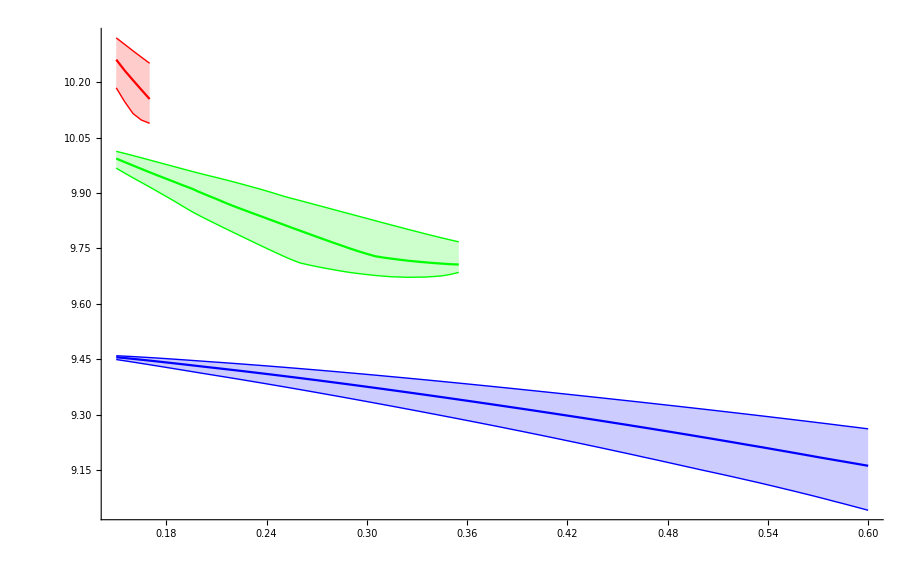

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;]],wrfitbb[[;;,1]]}],Transpose[{Tscanborig[[;;]],wrfitbbl[[;;,1]]}],Transpose[{Tscanborig[[;;]],wrfitbbu[[;;,1]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],wrfitbb[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],wrfitbbl[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],wrfitbbu[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],wrfitbb[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],wrfitbbl[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],wrfitbbu[[;;bb2uTcut-3,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/Upsilon1_mass.dat",Transpose[{Tscanborig,wrfitbb[[All,1]],wrfitbbl[[All,1]],wrfitbbu[[All,1]]}]]
```

plots/Upsilon1_mass.dat

```mathematica
Export["plots/Upsilon2_mass.dat",Transpose[{Tscanborig[[;;bb1uTcut-5]],wrfitbb[[;;bb1uTcut-5,2]],wrfitbbl[[;;bb1uTcut-5,2]],wrfitbbu[[;;bb1uTcut-5,2]]}]]
```

plots/Upsilon2_mass.dat

```mathematica
Export["plots/Upsilon3_mass.dat",Transpose[{Tscanborig[[;;bb2uTcut-3]],wrfitbb[[;;bb2uTcut-3,2]],wrfitbbl[[;;bb2uTcut-3,2]],wrfitbbu[[;;bb2uTcut-3,2]]}]]
```

plots/Upsilon3_mass.dat

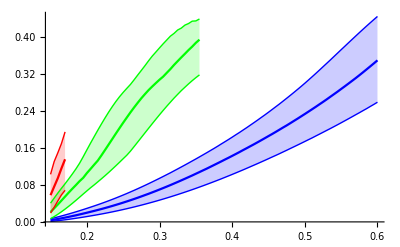

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;]],gfitbb[[;;,1]]}],Transpose[{Tscanborig[[;;]],gfitbbl[[;;,1]]}],Transpose[{Tscanborig[[;;]],gfitbbu[[;;,1]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],gfitbb[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],gfitbbl[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],gfitbbu[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],gfitbb[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],gfitbbl[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],gfitbbu[[;;bb2uTcut-3,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/Upsilon1_width.dat",Transpose[{Tscanborig,gfitbb[[All,1]],gfitbbl[[All,1]],gfitbbu[[All,1]]}]]
```

plots/Upsilon1_width.dat

```mathematica
Export["plots/Upsilon2_width.dat",Transpose[{Tscanborig[[;;bb1uTcut-5]],gfitbb[[;;bb1uTcut-5,2]],gfitbbl[[;;bb1uTcut-5,2]],gfitbbu[[;;bb1uTcut-5,2]]}]]
```

plots/Upsilon2_width.dat

```mathematica
Export["plots/Upsilon3_width.dat",Transpose[{Tscanborig[[;;bb2uTcut-3]],gfitbb[[;;bb2uTcut-3,2]],gfitbbl[[;;bb2uTcut-3,2]],gfitbbu[[;;bb2uTcut-3,2]]}]]
```

plots/Upsilon3_width.dat

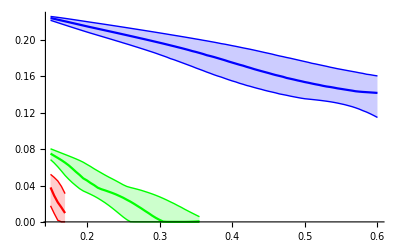

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;]],areafitbb[[;;,1]]}],Transpose[{Tscanborig[[;;]],areafitbbl[[;;,1]]}],Transpose[{Tscanborig[[;;]],areafitbbu[[;;,1]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],areafitbb[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],areafitbbl[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb1uTcut-5]],areafitbbu[[;;bb1uTcut-5,2]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],areafitbb[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],areafitbbl[[;;bb2uTcut-3,3]]}],Transpose[{Tscanborig[[;;bb2uTcut-3]],areafitbbu[[;;bb2uTcut-3,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/Upsilon1_area.dat",Transpose[{Tscanborig,areafitbb[[All,1]],areafitbbl[[All,1]],areafitbbu[[All,1]]}]]
```

plots/Upsilon1_area.dat

```mathematica
Export["plots/Upsilon2_area.dat",Transpose[{Tscanborig[[;;bb1uTcut-5]],areafitbb[[;;bb1uTcut-5,2]],areafitbbl[[;;bb1uTcut-5,2]],areafitbbu[[;;bb1uTcut-5,2]]}]]
```

plots/Upsilon2_area.dat

```mathematica
Export["plots/Upsilon3_area.dat",Transpose[{Tscanborig[[;;bb2uTcut-3]],areafitbb[[;;bb2uTcut-3,2]],areafitbbl[[;;bb2uTcut-3,2]],areafitbbu[[;;bb2uTcut-3,2]]}]]
```

plots/Upsilon3_area.dat

## Bottomonium p-wave

#### New fitting function

```mathematica
fitnew[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/50}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2]},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];
```

### Input data

```mathematica
Tscanborig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Do[bbdata[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

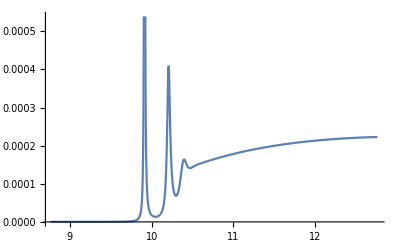

```mathematica
Block[{n=1},ListPlot[bbdata[n],Joined->True]]
```

```mathematica
Do[bbdatal[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

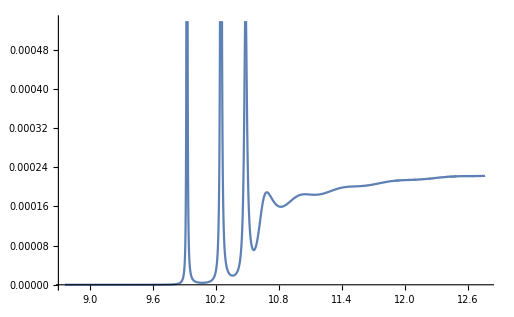

```mathematica
Block[{n=1},ListPlot[bbdatal[n],Joined->True]]
```

```mathematica
Do[bbdatau[n]=Import["bb/pwbbT"<>ToString[Round[1000 Tscanborig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b/a^2};,{n,Length[Tscanborig]}];
```

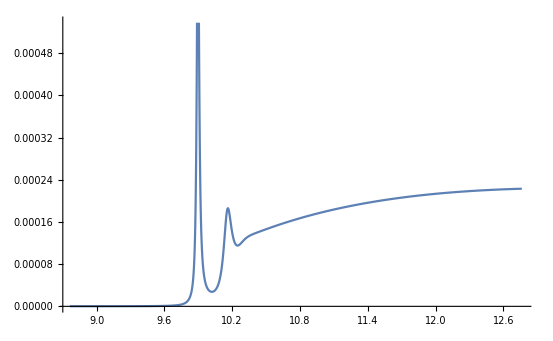

```mathematica
Block[{n=1},ListPlot[bbdatau[n],Joined->True]]
```

### Fitting

```mathematica
Clear[bbmodel,bbmodelu,bbmodell]
fitnew[bbdata,bbmodel,Tscanborig];
fitnew[bbdatau,bbmodelu,Tscanborig];
fitnew[bbdatal,bbmodell,Tscanborig];
```

### Store Results

```mathematica
Do[If[Length[bbmodel[[i]]]>4,bbmodel[[i]]=bbmodel[[i,;;4]]];If[Length[bbmodelu[[i]]]>4,bbmodelu[[i]]=bbmodelu[[i,;;4]]];If[Length[bbmodell[[i]]]>4,bbmodell[[i]]=bbmodell[[i,;;4]]];,{i,Length[bbmodel]}];
```

```mathematica
Clear[wrfitbbp,wrfitbbpl,wrfitbbpu,gfitbbp,gfitbbpl,gfitbbpu,areafitbbp,areafitbbpl,areafitbbpu,cfitbbp,cfitbbpl,cfitbbpu,dfitbbp,dfitbbpl,dfitbbpu,sfitbbp,sfitbbpl,sfitbbpu,s2fitbbp,s2fitbbpl,s2fitbbpu];
```

```mathematica
store[wr,wrfitbbp,bbmodel];
store[wr,wrfitbbpl,bbmodell];
store[wr,wrfitbbpu,bbmodelu];
store[Γ,gfitbbp,bbmodel];
store[Γ,gfitbbpl,bbmodell];
store[Γ,gfitbbpu,bbmodelu];
store[const,cfitbbp,bbmodel];
store[const,cfitbbpl,bbmodell];
store[const,cfitbbpu,bbmodelu];
store[δbg,dfitbbp,bbmodel];
store[δbg,dfitbbpl,bbmodell];
store[δbg,dfitbbpu,bbmodelu];
store[shift,sfitbbp,bbmodel];
store[shift,sfitbbpl,bbmodell];
store[shift,sfitbbpu,bbmodelu];
store[shift2,s2fitbbp,bbmodel];
store[shift2,s2fitbbpl,bbmodell];
store[shift2,s2fitbbpu,bbmodelu];
storearea[areafitbbp,bbmodel];
storearea[areafitbbpl,bbmodell];
storearea[areafitbbpu,bbmodelu];
```

### Display Results

```mathematica
import[wrfitbbp];
import[wrfitbbpl];
import[wrfitbbpu];
import[gfitbbp];
import[gfitbbpl];
import[gfitbbpu];
import[cfitbbp];
import[cfitbbpl];
import[cfitbbpu];
import[dfitbbp];
import[dfitbbpl];
import[dfitbbpu];
import[sfitbbp];
import[sfitbbpl];
import[sfitbbpu];
import[s2fitbbp];
import[s2fitbbpl];
import[s2fitbbpu];
import[areafitbbp];
import[areafitbbpl];
import[areafitbbpu];
```

```mathematica
Do[If[Length[wrfitbbp[[-i]]]<2,bb1Tcut=Length[wrfitbbp]-i];,{i,Length[wrfitbbp]}];
Do[If[Length[wrfitbbpu[[-i]]]<2,bb1uTcut=Length[wrfitbbpu]-i];,{i,Length[wrfitbbpu]}];
Do[If[Length[wrfitbbpl[[-i]]]<2,bb1lTcut=Length[wrfitbbpl]-i];,{i,Length[wrfitbbpl]}];
Do[If[Length[wrfitbbp[[-i]]]<3,bb2Tcut=Length[wrfitbbp]-i];,{i,Length[wrfitbbp]}];
Do[If[Length[wrfitbbpu[[-i]]]<3,bb2uTcut=Length[wrfitbbpu]-i];,{i,Length[wrfitbbpu]}];
Do[If[Length[wrfitbbpl[[-i]]]<3,bb2lTcut=Length[wrfitbbpl]-i];,{i,Length[wrfitbbpl]}];
Do[If[Length[wrfitbbp[[-i]]]<4,bb3Tcut=Length[wrfitbbp]-i];,{i,Length[wrfitbbp]}];Do[If[Length[wrfitbbpu[[-i]]]<4,bb3uTcut=Length[wrfitbbpu]-i];,{i,Length[wrfitbbpu]}];Do[If[Length[wrfitbbpl[[-i]]]<4,bb3lTcut=Length[wrfitbbpl]-i];,{i,Length[wrfitbbpl]}];
```

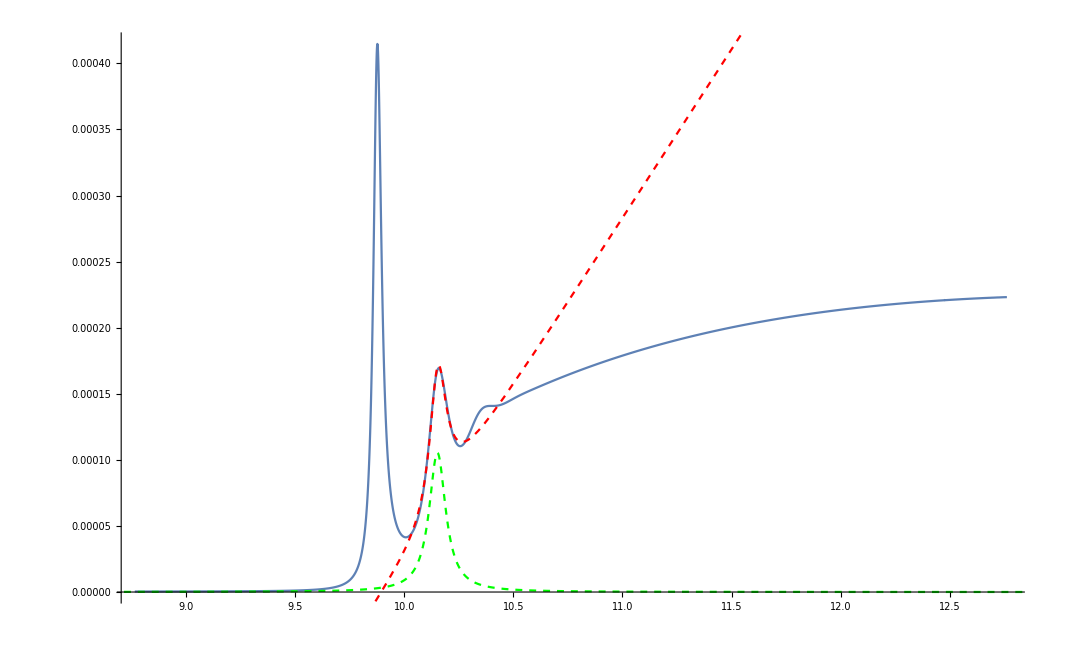

```mathematica
Block[{i=17,ii=2},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbbp[[i,ii]],gfitbbp[[i,ii]],dfitbbp[[i,ii]],cfitbbp[[i,ii]],sfitbbp[[i,ii]],s2fitbbp[[i,ii]]],{x,0.7wrfitbbp[[i,ii]],1.3wrfitbbp[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbp[[i,ii]],gfitbbp[[i,ii]],cfitbbp[[i,ii]]],{x,0.7wrfitbbp[[i,ii]],1.3wrfitbbp[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

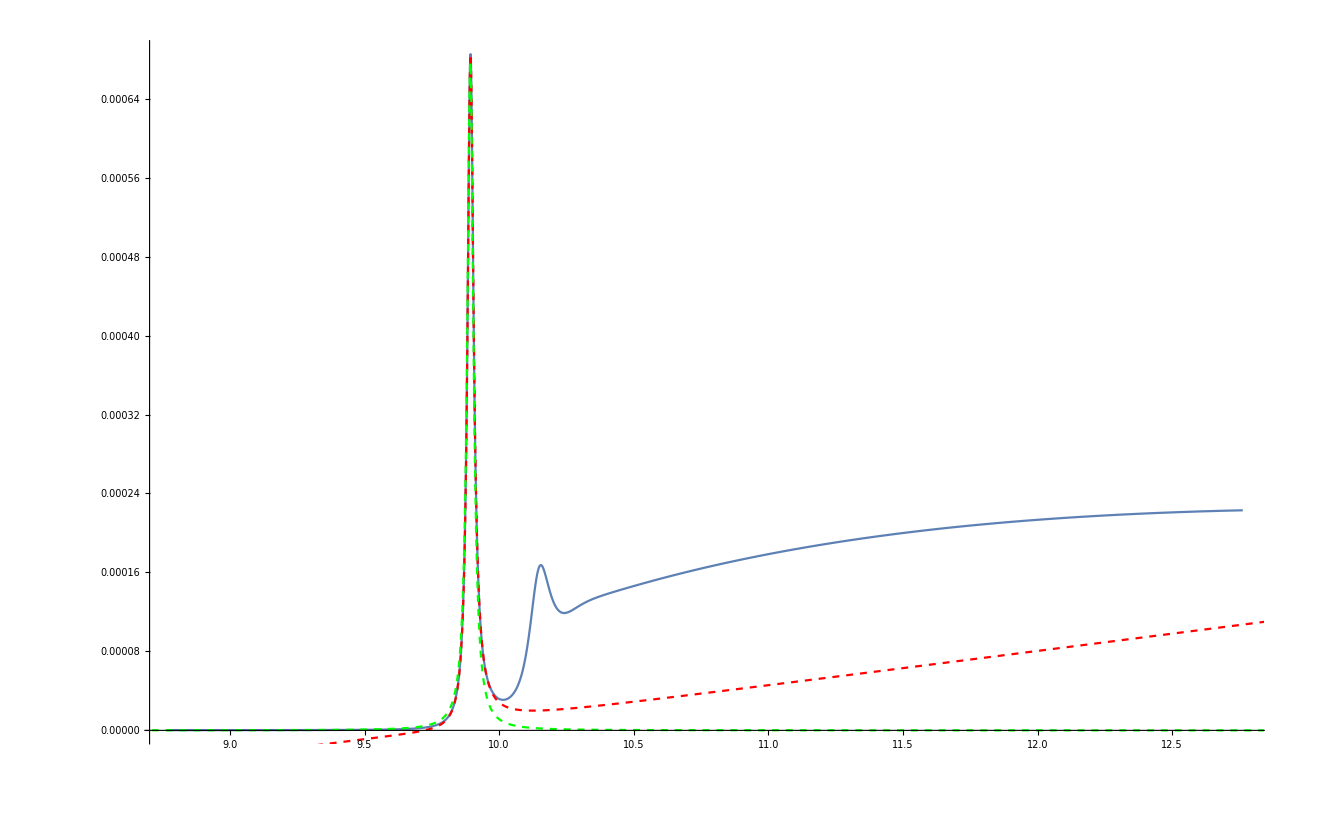

```mathematica
Block[{i=3,ii=1},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbpu[[i,ii]],gfitbbpu[[i,ii]],dfitbbpu[[i,ii]],cfitbbpu[[i,ii]],sfitbbpu[[i,ii]],s2fitbbpu[[i,ii]]],{x,0.7wrfitbbpu[[i,ii]],1.3wrfitbbpu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbpu[[i,ii]],gfitbbpu[[i,ii]],cfitbbpu[[i,ii]]],{x,0.7wrfitbbpu[[i,ii]],1.3wrfitbbpu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

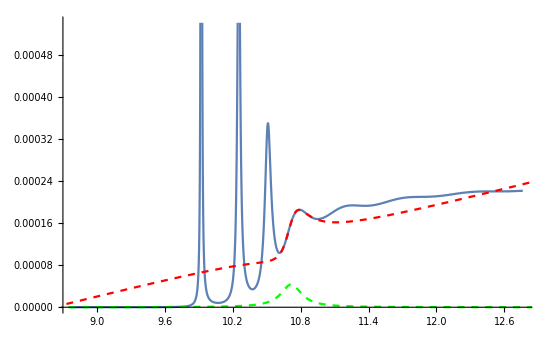

```mathematica
Block[{i=3,ii=4},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbpl[[i,ii]],gfitbbpl[[i,ii]],dfitbbpl[[i,ii]],cfitbbpl[[i,ii]],sfitbbpl[[i,ii]],s2fitbbpl[[i,ii]]],{x,0.7wrfitbbpl[[i,ii]],1.3wrfitbbpl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbpl[[i,ii]],gfitbbpl[[i,ii]],cfitbbpl[[i,ii]]],{x,0.7wrfitbbpl[[i,ii]],1.3wrfitbbpl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
bbcont={10.425372529034668,10.404981214520092,10.385922026714889,10.368044091781734,10.35121947718131,10.335338891872635,10.320308334354927,10.306046452794938,10.292482437343601,10.27955432217868,10.26720761394349,10.24407130162224,10.212685292903828,10.184560231890025,10.159082313112487,10.135789302532517,10.114325520768007,10.094412161602595,10.07582713164309,10.058390999148473,10.041956979744013,10.026403654258734,10.011629580012245,9.997549239631535,9.984089951820716,9.971438942026525,9.959680789921435,9.948305854630748,9.937283518695521,9.926586581618311,9.916190780073867,9.906074389122518,9.89621788725859,9.886603674129436,9.877215831435958,9.868039919223618,9.85906280330987,9.85027250500583,9.841658068570851,9.833209456470904,9.82491744608742,9.816773546416721,9.80876992739373,9.800899348409965,9.793155107173513,9.785530984945733,9.778021202444839,9.770620382177347,9.763323508502864,9.75612590137745,9.749023182471154,9.742011254470896,9.735086274550136,9.728244636109546,9.72148294899774,9.714798023963505,9.708186854179708,9.701646607145124};
```

```mathematica
bbcontl={10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.564,10.558776803262628,10.538134878500378,10.500489658120484,10.451414290636967,10.409208326874923,10.372286761717774,10.339533984651169,10.310139129414406,10.283496863363847,10.259144963513002,10.236723583223775,10.215947838507244,10.196588855570774,10.17846036007962,10.161408990613678,10.145307173449007,10.130393224425733,10.116761127143775,10.103691628392824,10.091134618659027,10.079046142722639,10.067387455668626,10.056124251413983,10.045226025730514,10.034665547681213,10.024418418371,10.014462700214768,10.004778606157178,9.995348233254255,9.986155331640164,9.977185119999842,9.968424110600633,9.959859967193557,9.951481384793144,9.943277972589815,9.9352401673584,9.927359144924983,9.919626748191943,9.91203542569425,9.904578168815082,9.897248468575935,9.890040263473244,9.88294790584187,9.875966121302445,9.86908997993277,9.862314866023546,9.855636453997409,9.84905068084264,9.842553732821019};
```

```mathematica
bbcontu={10.2240569943723,10.20971479010396,10.196101529694937,10.18314865391993,10.170796382257334,10.158992312756736,10.147690287745412,10.136849468780007,10.126433571037268,10.116410225511705,10.106750450059334,10.088420033357345,10.063077393588816,10.03990460603857,10.018537863136887,9.99869443617061,9.980150742536805,9.962727267888553,9.946277944509625,9.930682506060366,9.915840880865842,9.901669008656564,9.88809567258373,9.875060067035442,9.862509907136289,9.850605104485473,9.839421270863218,9.828542983226622,9.81794742279319,9.807614172072604,9.797524895428012,9.787663071080564,9.778013763794982,9.768563431619306,9.759299760827858,9.750211524163381,9.741288460056692,9.732521166440108,9.72390100612571,9.715420032652336,9.707070915275532,9.698846878804567,9.690741652470745,9.682749417019846,9.674864767619567,9.667082673025076,9.659398442882043,9.651807699761754,9.644306348933513,9.63689055892815,9.629556735615726,9.62230150674295,9.615121701552368,9.608014336921682,9.600976602143355,9.594005846989685,9.587099567370426,9.580255399164331};
```

```mathematica
Export["plots/chib_Econt.dat",Transpose[{Tscanborig,bbcont,bbcontl,bbcontu}]]
```

plots/chib_Econt.dat

```mathematica
bbbind=bbcont-wrfitbbp;
bbbindu=bbcontu-wrfitbbpu;
bbbindl=bbcontl-wrfitbbpl;
```

```mathematica
Do[If[(bbbind-gfitbbp)[[i,1]]>0,bb1Tmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbind-gfitbbp)[[i,2]]>0,bb2Tmelt=i],{i,1,bb1Tcut}];
Do[If[(bbbind-gfitbbp)[[i,3]]>0,bb3Tmelt=i],{i,1,bb2Tcut}];
Do[If[(bbbind-gfitbbp)[[i,4]]>0,bb4Tmelt=i,bb4Tmelt=1],{i,1,bb3Tcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Do[If[(bbbindu-gfitbbpu)[[i,1]]>0,bb1uTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindu-gfitbbpu)[[i,2]]>0,bb2uTmelt=i],{i,1,bb1uTcut}];
Do[If[(bbbindu-gfitbbpu)[[i,3]]>0,bb3uTmelt=i,bb3uTmelt=1],{i,1,bb2uTcut}];
bb4uTmelt=1;
Do[If[(bbbindu-gfitbbpu)[[i,4]]>0,bb4uTmelt=i],{i,1,bb3uTcut}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Do[If[(bbbindl-gfitbbpl)[[i,1]]>0,bb1lTmelt=i],{i,1,Length[bbbind]}];
Do[If[(bbbindl-gfitbbpl)[[i,2]]>0,bb2lTmelt=i],{i,1,bb1lTcut}];
Do[If[(bbbindl-gfitbbpl)[[i,3]]>0,bb3lTmelt=i],{i,1,bb2lTcut}];
Do[If[(bbbindl-gfitbbpl)[[i,4]]>0,bb4lTmelt=i,bb4lTmelt=1],{i,1,bb3lTcut}];
```

```mathematica
N[{Tscanborig[[bb1lTmelt-1]],Tscanborig[[bb1Tmelt]],Tscanborig[[bb1uTmelt]]}/0.155]
```

{1.64516,1.39355,1.21935}

```mathematica
N[{Tscanborig[[bb2lTmelt]],Tscanborig[[bb2Tmelt]],Tscanborig[[1]]}/0.155]
```

{1.18065,1.04516,0.967742}

```mathematica
N[{Tscanborig[[bb3lTmelt]],Tscanborig[[1]],Tscanborig[[1]]}/0.155]
```

{1.03226,0.967742,0.967742}

```mathematica
N[{Tscanborig[[bb4lTmelt]],Tscanborig[[1]],Tscanborig[[1]]}/0.155]
```

{0.967742,0.967742,0.967742}

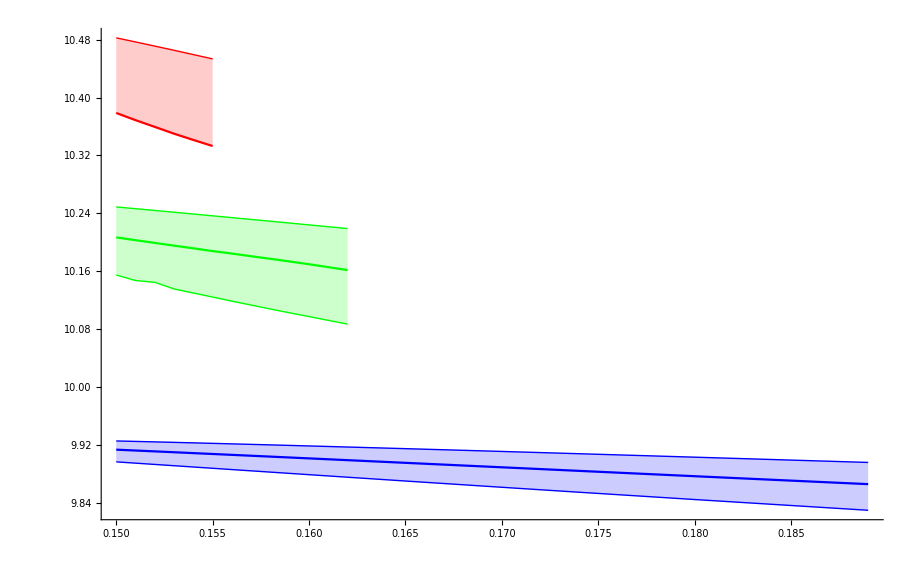

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbp[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbpl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbpu[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;12]],wrfitbbp[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],wrfitbbpl[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],wrfitbbpu[[;;12,2]]}],Transpose[{Tscanborig[[;;6]],wrfitbbp[[;;6,3]]}],Transpose[{Tscanborig[[;;6]],wrfitbbpl[[;;6,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/chib1_mass.dat",Transpose[{Tscanborig[[;;bb1uTmelt]],wrfitbbp[[;;bb1uTmelt,1]],wrfitbbpl[[;;bb1uTmelt,1]],wrfitbbpu[[;;bb1uTmelt,1]]}]]
```

plots/chib1_mass.dat

```mathematica
Export["plots/chib2_mass.dat",Transpose[{Tscanborig[[;;12]],wrfitbbp[[;;12,2]],wrfitbbpl[[;;12,2]],wrfitbbpu[[;;12,2]]}]]
```

plots/chib2_mass.dat

```mathematica
Export["plots/chib3_mass.dat",Transpose[{Tscanborig[[;;6]],wrfitbbp[[;;6,3]],wrfitbbpl[[;;6,3]]}]]
```

plots/chib3_mass.dat

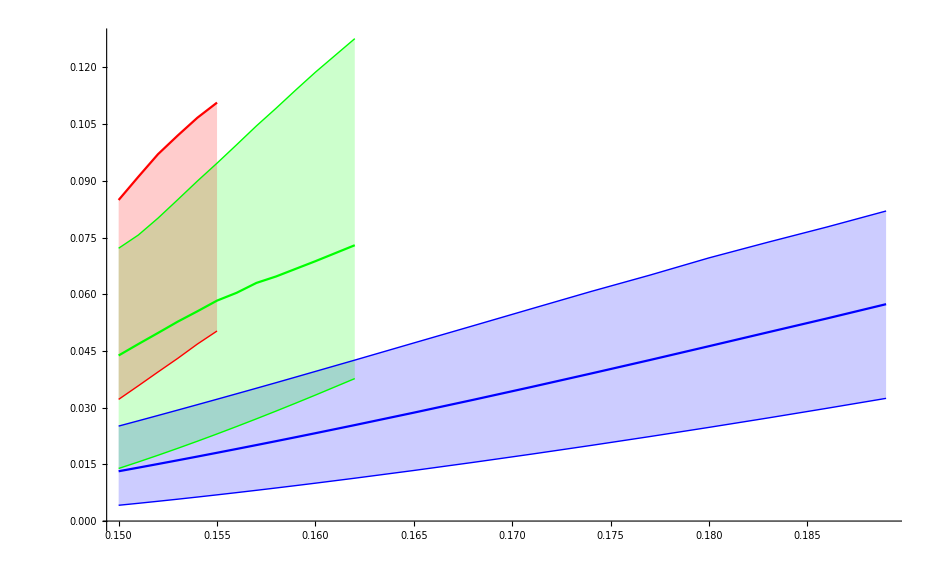

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbp[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbpl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbpu[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;12]],gfitbbp[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],gfitbbpl[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],gfitbbpu[[;;12,2]]}],Transpose[{Tscanborig[[;;6]],gfitbbp[[;;6,3]]}],Transpose[{Tscanborig[[;;6]],gfitbbpl[[;;6,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/chib1_width.dat",Transpose[{Tscanborig[[;;bb1uTmelt]],gfitbbp[[;;bb1uTmelt,1]],gfitbbpl[[;;bb1uTmelt,1]],gfitbbpu[[;;bb1uTmelt,1]]}]]
```

plots/chib1_width.dat

```mathematica
Export["plots/chib2_width.dat",Transpose[{Tscanborig[[;;12]],gfitbbp[[;;12,2]],gfitbbpl[[;;12,2]],gfitbbpu[[;;12,2]]}]]
```

plots/chib2_width.dat

```mathematica
Export["plots/chib3_width.dat",Transpose[{Tscanborig[[;;6]],gfitbbp[[;;6,3]],gfitbbpl[[;;6,3]]}]]
```

plots/chib3_width.dat

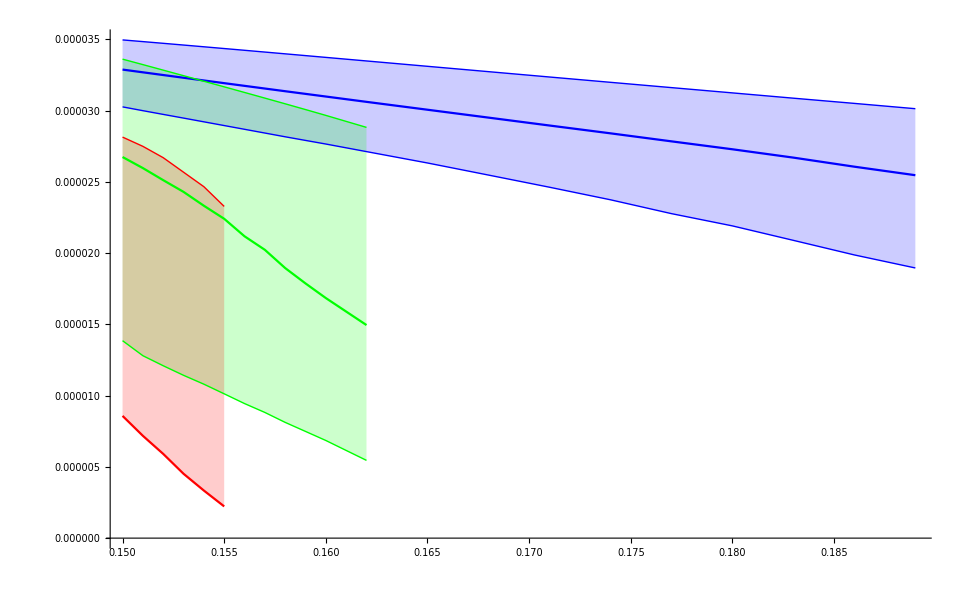

```mathematica
ListPlot[{Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbp[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbpl[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbpu[[;;bb1uTmelt,1]]}],Transpose[{Tscanborig[[;;12]],areafitbbp[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],areafitbbpl[[;;12,2]]}],Transpose[{Tscanborig[[;;12]],areafitbbpu[[;;12,2]]}],Transpose[{Tscanborig[[;;6]],areafitbbp[[;;6,3]]}],Transpose[{Tscanborig[[;;6]],areafitbbpl[[;;6,3]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin}},Joined->True]
```

```mathematica
Export["plots/chib1_area.dat",Transpose[{Tscanborig[[;;bb1uTmelt]],areafitbbp[[;;bb1uTmelt,1]],areafitbbpl[[;;bb1uTmelt,1]],areafitbbpu[[;;bb1uTmelt,1]]}]]
```

plots/chib1_area.dat

```mathematica
Export["plots/chib2_area.dat",Transpose[{Tscanborig[[;;12]],areafitbbp[[;;12,2]],areafitbbpl[[;;12,2]],areafitbbpu[[;;12,2]]}]]
```

plots/chib2_area.dat

```mathematica
Export["plots/chib3_area.dat",Transpose[{Tscanborig[[;;6]],areafitbbp[[;;6,3]],areafitbbpl[[;;6,3]]}]]
```

plots/chib3_area.dat